# SE Solutions in Regions of Constant Potential

## Constant Potential Solutions

```mathematica
Clear[Ψconst]
Ψconst[Eval_,V0_,sign_]:=
With[{k=π Sqrt[Eval-V0],ω=π Eval},
Function[{x,t},Exp[sign I k x]Exp[-I ω t]]
]
```

```mathematica
Clear[wfplot]
wfplot[Ψ_,t_,OptionsPattern[]]:=
With[{
xrange=OptionValue["xrange"],
yrange=OptionValue["yrange"],
label=OptionValue["label"],
npoints=OptionValue["npoints"],
padFraction=OptionValue["padFraction"],
verbose=OptionValue["verbose"],
gopts=OptionValue["gopts"],
normalize=OptionValue["normalize"]
},
Module[{xmin,xmax,x,re,im,absq,sumsq,all,ypad,ymin,ymax},
{xmin,xmax}=xrange;
x=Range[xmin,xmax,(xmax-xmin)/npoints];
re=Re[Ψ[x,t]];
im=Im[Ψ[x,t]];
absq=re^2+im^2;
If[normalize===True,
sumsq=Total[absq];
im/=sumsq;
re/=sumsq;
absq/=sumsq;
];
all=Join[re,im,absq];
If[yrange===Automatic,
ymin=Min[all];
ymax=Max[all];
ypad=padFraction (ymax-ymin);
ymin -= ypad;
ymax += ypad;
If[verbose===True,Print["yrange->",{ymin,ymax}]];
,
{ymin,ymax}=yrange
];
ListPlot[{
Transpose[{x,re}],Transpose[{x,im}],Transpose[{x,absq}]
},gopts,
Joined->True,PlotStyle->{Directive[Thick,Red,Opacity[0.75]],Directive[Thick,Blue,Opacity[0.75]],Directive[Thick,Black]},Filling->{3->0},FillingStyle->Directive[Black,Opacity[0.1]],PlotRange->{{xmin,xmax},{ymin,ymax}},Frame->True,FrameTicks->None,AspectRatio->Full,Epilog->If[label===None,{},
{Text[Style[label,FontSize->Large,FontFamily->"Helvetica",FontWeight->"Bold"],Scaled[{0.5,0.0}],{0,-1}]}
]]
]
]
Options[wfplot]={"label"->None,"xrange"->{-1,+1},"yrange"->Automatic,"npoints"->1000,"padFraction"->0.05,"verbose"->False,"gopts"->{},"normalize"->False};
```

yrange->{-0.0010989,0.0010989}

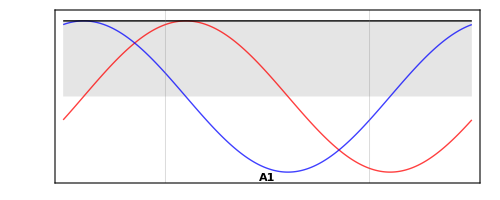

```mathematica
wfplot[Ψconst[+2,+1,-1],0.2,"xrange"->{-1,+1},"yrange"->Automatic,"label"->"A1","verbose"->True,"gopts"->{Axes->{Automatic,None},GridLines->{{-0.5,+0.5},None}},"normalize"->True]
```

```mathematica
Clear[plotAll]
plotAll[t_,margin_:4]:=
With[{
opt={"xrange"->{-1,+1},"yrange"->{-1.2,+1.2}}
},
GraphicsGrid[
{
{
wfplot[Ψconst[+2,+1,-1],t,label->"A1",opt],
wfplot[Ψconst[+2,+1,+1],t,label->"A2",opt],
wfplot[Ψconst[-2,-1,-1],t,label->"A3",opt],
wfplot[Ψconst[-2,-1,+1],t,label->"A4",opt]
},
{
wfplot[Ψconst[+1,0,-1],t,label->"B1",opt],
wfplot[Ψconst[+1,0,+1],t,label->"B2",opt],
wfplot[Ψconst[-1,0,-1],t,label->"B3",opt],
wfplot[Ψconst[-1,0,+1],t,label->"B4",opt]
},
{
wfplot[Ψconst[+2,0,-1],t,label->"C1",opt],
wfplot[Ψconst[+2,0,+1],t,label->"C2",opt],
wfplot[Ψconst[-2,0,-1],t,label->"C3",opt],
wfplot[Ψconst[-2,0,+1],t,label->"C4",opt]
}
},
ImageSize->{1024-2margin,768-2margin},AspectRatio->Full,ImageMargins->margin
]
]
```

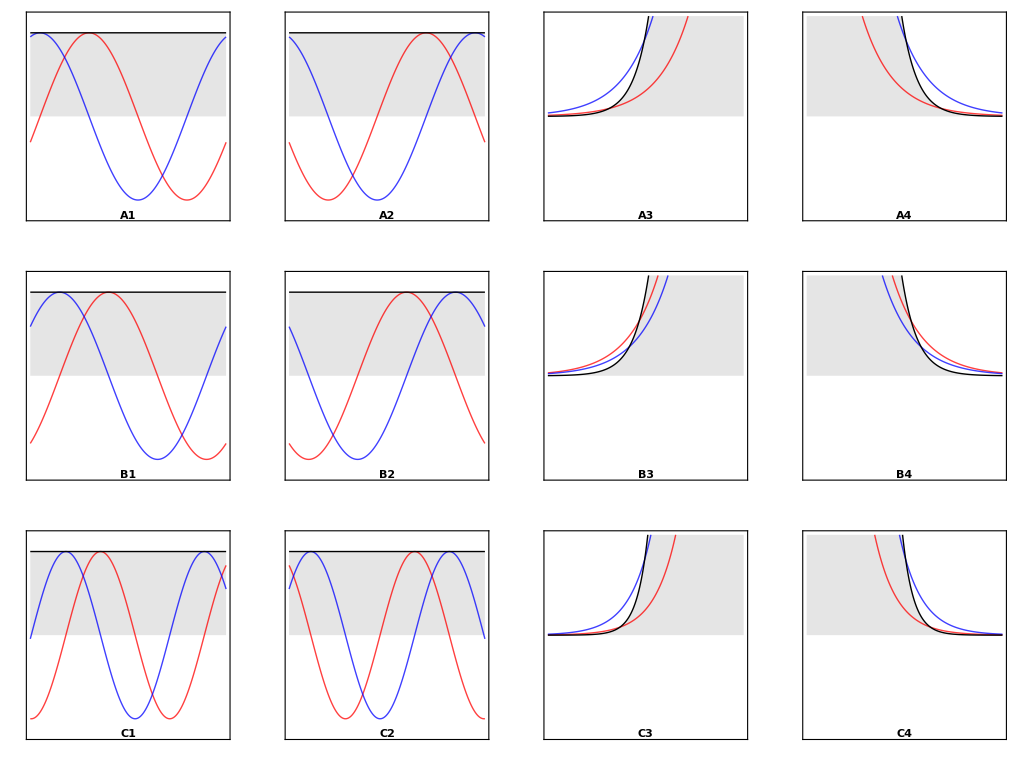

```mathematica
plotAll[0.2]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/V0solns.pdf",plotAll[0.2]]
```

/Users/david/Documents/uci/Teaching/113A/Activities/V0solns.pdf

```mathematica
With[{nframes=150},
Timing[frames=Table[plotAll[2 (n/nframes)],{n,0,nframes-1}];]
]
```

{30.9051,Null}

```mathematica
Export["/Users/david/Desktop/V0solns.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"->1/30]
```

/Users/david/Desktop/V0solns.gif

## Scattering with Finite Step Potentials

```mathematica
Clear[finiteStep]
finiteStep[Eval_,Va_,Vb_,Vc_,OptionsPattern[]]:=
With[{
direction=OptionValue["direction"],
ka=π Sqrt[Eval-Va],
kb=π Sqrt[Eval-Vb],
kc=π Sqrt[Eval-Vc],
ω=π Eval,
xab=-1,
xbc=+1
},
Module[{ψa,ψb,ψc,ap,am,bp,bm,cp,cm,soln,ψabc,Ψ,V,fixed,floating,eqns},
ψa=Function[x,ap Exp[I ka x]+am Exp[-I ka x]];
ψb=Function[x,bp Exp[I kb x]+bm Exp[-I kb x]];
ψc=Function[x,cp Exp[I kc x]+cm Exp[-I kc x]];
If[direction==="left",
fixed={ap->0,cm->1},
fixed={ap->1,cm->0}
];
floating={am,bp,bm,cp};
eqns=Simplify[{
ψa[xab]==ψb[xab],
ψb[xbc]==ψc[xbc],
ψa'[xab]==ψb'[xab],
ψb'[xbc]==ψc'[xbc]
}/.fixed];
soln=Simplify[First[Solve[eqns,floating]]];
ψabc=Function[x,
Evaluate[N[
UnitStep[xab-x]ψa[x]+(1-UnitStep[xab-x])(1-UnitStep[x-xbc])ψb[x]+UnitStep[x-xbc]ψc[x]/.fixed/.soln
]]
];
Ψ=Function[{x,t},ψabc[x]Exp[-I ω t]];
V=Function[x,UnitStep[xab-x]Va+(1-UnitStep[xab-x])(1-UnitStep[x-xbc])Vb+UnitStep[x-xbc]Vc];
Return[{Ψ,V}]
]
]
Options[finiteStep]={"direction"->"right"};
```

```mathematica
Clear[Vplot]
Vplot[V_,Eval_,OptionsPattern[]]:=
With[{
xrange=OptionValue["xrange"],
yrange=OptionValue["yrange"],
label=OptionValue["label"]
},
Module[{xmin,xmax},
{xmin,xmax}=xrange;
Plot[
{V[x],Eval},{x,xmin,xmax},
Filling->{1->Bottom},PlotStyle->{Automatic,Directive[Red,Dashed]},PlotRange->{xrange,yrange},Frame->True,LabelStyle->Medium,FrameLabel->{"Position x [arb.units]","Potential energy V(x) [arb.units]"},AspectRatio->Full,Epilog->If[label===None,{},
{Text[Style[label,FontSize->Large,FontFamily->"Helvetica",FontWeight->"Bold"],Scaled[{0.5,0.0}],{0,-1}]}
]
]
]
]
Options[Vplot]={"xrange"->{-1,+1},"yrange"->{-1,+1},"label"->None};
```

```mathematica
With[{
opts={
"xrange"->{-3,3},
"yrange"->{-0.0016,+0.0038},
"normalize"->True,
"gopts"->{Axes->{Automatic,None},GridLines->{{-1,+1},None},GridLinesStyle->Directive[Black,Dashed]}
},
margin=4,
EA=1,
EB=2,
nframes=150
},
Module[{ΨA1,ΨA2,ΨA3,ΨB1,ΨB2,ΨB3,V1,V2,V3,plot,vopts,vplot},
{ΨA1,V1}=finiteStep[EA,0,1.01,0];
{ΨB1,V1}=finiteStep[EB,0,1.01,0];
{ΨA2,V2}=finiteStep[EA,0.5,0,0.5];
{ΨB2,V2}=finiteStep[EB,0.5,0,0.5];
{ΨA3,V3}=finiteStep[EA,1.2,0.6,0,"direction"->"left"];
{ΨB3,V3}=finiteStep[EB,1.2,0.6,0,"direction"->"left"];
plot=Function[t,
GraphicsGrid[
{
{
wfplot[ΨA1,t,label->"A1",opts],
wfplot[ΨA2,t,label->"A2",opts],
wfplot[ΨA3,t,label->"A3",opts]
},
{
wfplot[ΨB1,t,label->"B1",opts],
wfplot[ΨB2,t,label->"B2",opts],
wfplot[ΨB3,t,label->"B3",opts]
}
},
ImageSize->{1024-2 margin,768-2margin},ImageMargins->margin,AspectRatio->Full
]
];
(* Save a still frame for the handout *)
Export["/Users/david/Desktop/stepPsiFrame.pdf",plot[0.2]];
(* Save the animated frames *)
Print[Timing[frames=Table[plot[2 (n/nframes)],{n,0,nframes-1}];]];
Export["/Users/david/Desktop/stepPsi.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"->1/30];
(* Save the solution *)
vopts={"xrange"->{-3,3},"yrange"->{-0.1,2.1}};
vplot=GraphicsGrid[
{
{
Vplot[V1,EA,label->"A1",vopts],
Vplot[V2,EA,label->"A2",vopts],
Vplot[V3,EA,label->"A3",vopts]
},
{
Vplot[V1,EB,label->"B1",vopts],
Vplot[V2,EB,label->"B2",vopts],
Vplot[V3,EB,label->"B3",vopts]
}
},
ImageSize->{1024-2 margin,768-2margin},ImageMargins->margin,AspectRatio->Full,Spacings->2
];
Export["/Users/david/Desktop/stepV.png",vplot];
]
]
```

{109.145,Null}

## Bound States

```mathematica
Clear[boundState]
boundState[Eval_,Va_,Vb_,Vc_]:=
With[{
κa=π Sqrt[Va-Eval],
kb=π Sqrt[Eval-Vb],
κc=π Sqrt[Vc-Eval],
ω=π Eval,
xab=-1,
xbc=+1
},
Module[{ψa,ψb,ψc,am,bm,cp,soln,sign,ψab,V,floating,eqns},
ψa=Function[x,am Exp[+κa x]];
ψb=Function[x,Cos[kb x]+ bm Sin[kb x]];
ψc=Function[x,cp Exp[-κc x]];
floating={am,bm,cp};
eqns=Simplify[{
ψa[xab]==ψb[xab],
(*ψb[xbc]==ψc[xbc],*)
ψa'[xab]==ψb'[xab],
ψb'[xbc]==ψc'[xbc]
}];
soln=Simplify[First[Solve[eqns,floating]]];
(* Pick the overall sign so that ψa[xab] > 0 *)
sign=Sign[ψa[xab]/.soln];
ψab=Function[x,
Evaluate[N[
sign(UnitStep[xab-x]ψa[x]+(1-UnitStep[xab-x])ψb[x])/.soln
]]
];
ψc=Function[x,Evaluate[N[sign ψc[x]/.soln]]];
V=Function[x,UnitStep[xab-x]Va+(1-UnitStep[xab-x])(1-UnitStep[x-xbc])Vb+UnitStep[x-xbc]Vc];
Return[{ψab,ψc,V,xbc}]
]
]
```

```mathematica
boundStatePlot[Eval_,Va_,Vb_,Vc_,t_]:=
With[{
xrange={-3,+3},
Vrange={-0.1,3.1}
},
Module[{ψab,ψc,V,xbc,ψabPts,ψcPts},
{ψab,ψc,V,xbc}=boundState[Eval,Va,Vb,Vc];
ψabPts=Table[{x,ψab[x]},{x,-3,xbc,0.01}];
ψcPts=Table[{x,ψc[x]},{x,xbc,+3,0.01}];
GraphicsRow[{
Show[{
ListPlot[ψabPts,PlotRange->{xrange,Automatic},Joined->True,Frame->True,FrameLabel->{"Position x [arb.units]","Reψ(x)"},
Axes->{Automatic,None},FrameTicks->None,GridLines->{{-1,+1},None},GridLinesStyle->Directive[Black,Dashed],PlotStyle->Directive[Thick,Red],AspectRatio->Full,LabelStyle->Medium],
ListPlot[ψcPts,PlotRange->All,Joined->True,PlotStyle->Directive[Thick,Red,Dashed]]
}],
Plot[
{V[x],Eval},{x,-3,+3},
Filling->{1->Bottom},PlotStyle->{Automatic,Directive[Darker[Green],Dashed]},PlotRange->{xrange,Vrange},Frame->True,LabelStyle->Medium,FrameTicks->None,FrameLabel->{"Position x [arb.units]","Potential,total energy V(x) [arb.units]"},AspectRatio->Full]
},
AspectRatio->Full
]
]
]
```

```mathematica
Manipulate[GraphicsGrid[{
{boundStatePlot[Eval,3,0,2,0]},
{boundStatePlot[Eval,2,0,2,0]},
{boundStatePlot[Eval,2,0,3,0]}
},ImageSize->{1024,768},AspectRatio->Full],
{Eval,0.01,1.99}
]
```

```mathematica
Timing[frames=
With[{nframes=150},
Table[GraphicsGrid[{
{boundStatePlot[Eval,3,0,2,0]},
{boundStatePlot[Eval,2,0,2,0]},
{boundStatePlot[Eval,2,0,3,0]}
},ImageSize->{1024,768},AspectRatio->Full],
{Eval,0.01,1.99,1.98/nframes}
]
];
]
```

{20.137,Null}

```mathematica
Export["/Users/david/Desktop/stepBound.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"->1/10];
```

```mathematica
Export["/Users/david/Desktop/stepBoundFrame.pdf",frames[[112]]]
```

/Users/david/Desktop/stepBoundFrame.pdf

## Activity 9 Graphs

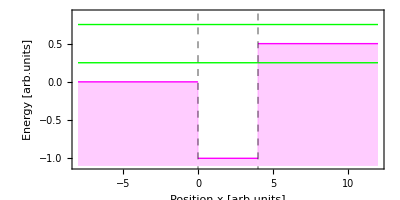

```mathematica
scatter1=With[{
V=Function[x,Piecewise[{{0,x<0},{-1,x<4}},0.5]],
E1=0.25,
E2=0.75
},
Plot[{V[x],E1,E2},{x,-8,12},Frame->True,FrameLabel->{"Position x [arb.units]","Energy [arb.units]"},PlotStyle->{Directive[Thick,Magenta],Directive[Thick,Green],Directive[Thick,Green]},Filling->{1->Bottom},PlotRange->{{-8,12},{-1.1,0.9}},Axes->None,GridLines->{{0,4},None},GridLinesStyle->Directive[Black,Dashed],AspectRatio->1/2]
]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/scatter1.pdf",scatter1]
```

/Users/david/Documents/uci/Teaching/113A/Activities/scatter1.pdf

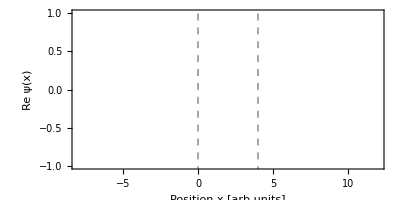

```mathematica
scatter2=Plot[{},{x,-8,12},Frame->True,FrameLabel->{"Position x [arb.units]","Re ψ(x)"},PlotStyle->{Directive[Thick,Magenta],Directive[Thick,Green],Directive[Thick,Green]},Filling->{1->Bottom},PlotRange->{{-8,12},{-1,+1}},Axes->{Automatic,None},GridLines->{{0,4},None},GridLinesStyle->Directive[Black,Dashed],AspectRatio->1/2]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/scatter2.pdf",scatter2]
```

/Users/david/Documents/uci/Teaching/113A/Activities/scatter2.pdf

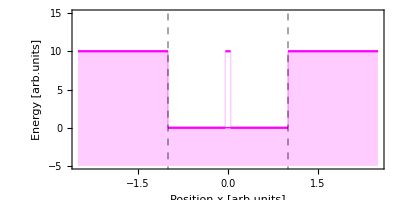

```mathematica
bound1=With[{
V1=Function[x,Piecewise[{{10,x<-1},{0,x<+1}},10]],
V2=Function[x,Piecewise[{{10,x<-1},{0,x<-0.045},{10,x<+0.045},{0,x<1}},10]]
},
Plot[{V1[x],V2[x]},{x,-2.5,2.5},Frame->True,FrameLabel->{"Position x [arb.units]","Energy [arb.units]"},PlotPoints->400,PlotStyle->{Directive[Thick,Magenta],Directive[Medium,Magenta]},Filling->{1->Bottom},PlotRange->{{-2.5,2.5},{-5,15}},Axes->None,GridLines->{{-1,+1},None},GridLinesStyle->Directive[Black,Dashed],AspectRatio->1/2]
]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/bound1.pdf",bound1]
```

/Users/david/Documents/uci/Teaching/113A/Activities/bound1.pdf

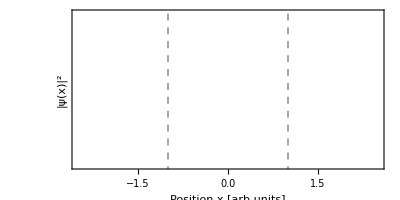

```mathematica
bound2=Plot[{},{x,-2.5,2.5},Frame->True,FrameLabel->{"Position x [arb.units]","|ψ(x)|^2"},PlotStyle->{Directive[Thick,Magenta],Directive[Thick,Green],Directive[Thick,Green]},Filling->{1->Bottom},FrameTicks->{Automatic,None},PlotRange->{{-2.5,2.5},{0,1}},Axes->{Automatic,None},GridLines->{{-1,+1},None},GridLinesStyle->Directive[Black,Dashed],AspectRatio->1/2]
```

```mathematica
Export["/Users/david/Documents/uci/Teaching/113A/Activities/bound2.pdf",bound2]
```

/Users/david/Documents/uci/Teaching/113A/Activities/bound2.pdf